# Assignment 10 - Cameron Embree

Assignment 9 - Due April 7

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets the directory to look for files to the same directory the notebook (this file) is in*)
rawdata=Import["Constitutional_Convention_Votes.csv"];
(*votecodes 1 -> Yea, 0 -> Nay, 6-> Abstain*)
```

```mathematica
statePostCode=Table[rawdata[[i,1]],{i,1,rawdata//Length}]
```

{NH,MA,CT,NY,NJ,PA,DE,MD,VA,NC,SC,GA}

```mathematica
(*
both=Flatten[Join[Position[rawdata[[1,All]],1],Position[rawdata[[2,All]],1]]]//Tally
same=Select[both,#[[2]]>1&]
same//Length
*)

psim[i_,j_]:=Module[{},
combinedTotNonAbstained=Flatten[Join[
Position[rawdata[[i,All]],0],Position[rawdata[[i,All]],1],
Position[rawdata[[j,All]],0],Position[rawdata[[j,All]],1]]]//Tally;
same=Select[combinedTotNonAbstained,#[[2]]>1&];
Length[same]/Length[combinedTotNonAbstained]//N
]


datSize=rawdata//Length;
A=Table[psim[i,j],{i,1,datSize},{j,1,datSize}]
```

{{1.,0.636971,0.556277,0.618629,0.572632,0.592751,0.557895,0.543788,0.554415,0.578838,0.600877,0.591966},{0.636971,1.,0.510689,0.540441,0.492135,0.56974,0.5,0.473799,0.549425,0.595294,0.578049,0.576471},{0.556277,0.510689,1.,0.516605,0.528302,0.496536,0.48037,0.525463,0.481982,0.497738,0.484706,0.513889},{0.618629,0.540441,0.516605,1.,0.588785,0.559633,0.561111,0.582721,0.577982,0.597043,0.53407,0.585185},{0.572632,0.492135,0.528302,0.588785,1.,0.495575,0.545035,0.526667,0.462687,0.471215,0.448352,0.542986},{0.592751,0.56974,0.496536,0.559633,0.495575,1.,0.552204,0.526667,0.633333,0.516484,0.49095,0.512195},{0.557895,0.5,0.48037,0.561111,0.545035,0.552204,1.,0.574074,0.485777,0.465665,0.432967,0.461039},{0.543788,0.473799,0.525463,0.582721,0.526667,0.526667,0.574074,1.,0.559284,0.49467,0.447084,0.519737},{0.554415,0.549425,0.481982,0.577982,0.462687,0.633333,0.485777,0.559284,1.,0.598174,0.510158,0.57631},{0.578838,0.595294,0.497738,0.597043,0.471215,0.516484,0.465665,0.49467,0.598174,1.,0.57243,0.60739},{0.600877,0.578049,0.484706,0.53407,0.448352,0.49095,0.432967,0.447084,0.510158,0.57243,1.,0.654229},{0.591966,0.576471,0.513889,0.585185,0.542986,0.512195,0.461039,0.519737,0.57631,0.60739,0.654229,1.}}

6.+(0.636971-√((x[1,1]-x[2,1])^2))^2+(0.556277-√((x[1,1]-x[3,1])^2))^2+(0.510689-√((x[2,1]-x[3,1])^2))^2+(0.618629-√((x[1,1]-x[4,1])^2))^2+(0.540441-√((x[2,1]-x[4,1])^2))^2+(0.516605-√((x[3,1]-x[4,1])^2))^2+(0.572632-√((x[1,1]-x[5,1])^2))^2+(0.492135-√((x[2,1]-x[5,1])^2))^2+(0.528302-√((x[3,1]-x[5,1])^2))^2+(0.588785-√((x[4,1]-x[5,1])^2))^2+(0.592751-√((x[1,1]-x[6,1])^2))^2+(0.56974-√((x[2,1]-x[6,1])^2))^2+(0.496536-√((x[3,1]-x[6,1])^2))^2+(0.559633-√((x[4,1]-x[6,1])^2))^2+(0.495575-√((x[5,1]-x[6,1])^2))^2

{7.02674,{x[1,1]→0.629134,x[2,1]→0.37893,x[3,1]→-0.12571,x[4,1]→0.21725,x[5,1]→-0.313314,x[6,1]→0.0112555,x[7,1]→-0.0473402,x[8,1]→-0.315691,x[9,1]→0.0760784,x[10,1]→0.154964,x[11,1]→0.103122,x[12,1]→-0.144463,x[13,1]→0.624741}}

{x[1,1],x[2,1],x[3,1],x[4,1],x[5,1],x[6,1],x[7,1],x[8,1],x[9,1],x[10,1],x[11,1],x[12,1],x[13,1]}

{{0.629134},{0.37893},{-0.12571},{0.21725},{-0.313314},{0.0112555},{-0.0473402},{-0.315691},{0.0760784},{0.154964},{0.103122},{-0.144463}}

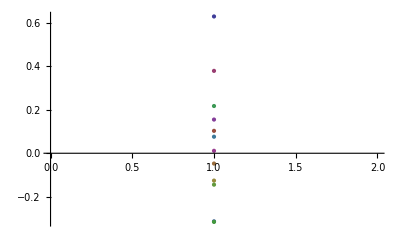

```mathematica
(*stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2+(x[i,2]-x[j,2])^2]+A[[i,j]])^2,{i,n},{j,i,n}]
*)
stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2]+A[[i,j]])^2,{i,n},{j,i,n}]
mds=NMinimize[stress,Flatten[Table[x[i,j],{i,13},{j,1}]]]

Flatten[Table[x[i,j],{i,13},{j,1}]]

(*Print["W/O: ",p=mds[[2,All,-1]]]
Print["PAR: ",p=Partition[mds[[2,All,-1]],1]]*)
p=Partition[mds[[2,All,-1]],1];
a=Table[Tooltip[p[[i]],statePostCode[[i]]],{i,1,statePostCode//Length}]

ListPlot[a]
```

6.+(0.636971-√((x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2))^2+(0.556277-√((x[1,1]-x[3,1])^2+(x[1,2]-x[3,2])^2))^2+(0.510689-√((x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2))^2+(0.618629-√((x[1,1]-x[4,1])^2+(x[1,2]-x[4,2])^2))^2+(0.540441-√((x[2,1]-x[4,1])^2+(x[2,2]-x[4,2])^2))^2+(0.516605-√((x[3,1]-x[4,1])^2+(x[3,2]-x[4,2])^2))^2+(0.572632-√((x[1,1]-x[5,1])^2+(x[1,2]-x[5,2])^2))^2+(0.492135-√((x[2,1]-x[5,1])^2+(x[2,2]-x[5,2])^2))^2+(0.528302-√((x[3,1]-x[5,1])^2+(x[3,2]-x[5,2])^2))^2+(0.588785-√((x[4,1]-x[5,1])^2+(x[4,2]-x[5,2])^2))^2+(0.592751-√((x[1,1]-x[6,1])^2+(x[1,2]-x[6,2])^2))^2+(0.56974-√((x[2,1]-x[6,1])^2+(x[2,2]-x[6,2])^2))^2+(0.496536-√((x[3,1]-x[6,1])^2+(x[3,2]-x[6,2])^2))^2+(0.559633-√((x[4,1]-x[6,1])^2+(x[4,2]-x[6,2])^2))^2+(0.495575-√((x[5,1]-x[6,1])^2+(x[5,2]-x[6,2])^2))^2

{6.2784,{x[1,1]→0.165115,x[1,2]→-0.194296,x[2,1]→0.337662,x[2,2]→0.519341,x[3,1]→0.0434821,x[3,2]→0.16611,x[4,1]→-0.283725,x[4,2]→0.186123,x[5,1]→0.444791,x[5,2]→0.196027,x[6,1]→-0.0481236,x[6,2]→0.54193,x[7,1]→-0.0130309,x[7,2]→0.077637,x[8,1]→-0.109334,x[8,2]→0.291718,x[9,1]→-0.0867994,x[9,2]→0.149339,x[10,1]→0.115576,x[10,2]→-0.000174926,x[11,1]→0.325284,x[11,2]→0.0248757,x[12,1]→0.360061,x[12,2]→0.502288,x[13,1]→0.243799,x[13,2]→0.0189905}}

{{0.165115,-0.194296},{0.337662,0.519341},{0.0434821,0.16611},{-0.283725,0.186123},{0.444791,0.196027},{-0.0481236,0.54193},{-0.0130309,0.077637},{-0.109334,0.291718},{-0.0867994,0.149339},{0.115576,-0.000174926},{0.325284,0.0248757},{0.360061,0.502288}}

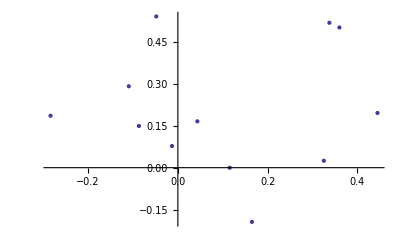

```mathematica
stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2+(x[i,2]-x[j,2])^2]+A[[i,j]])^2,{i,n},{j,i,n}]
mds=NMinimize[stress,Flatten[Table[x[i,j],{i,13},{j,2}]]]

p=Partition[mds[[2,All,-1]],2];
a=Table[Tooltip[p[[i]],statePostCode[[i]]],{i,1,statePostCode//Length}]

ListPlot[a]
```

```mathematica
stress=Sum[(-Sqrt[(x[i,1]-x[j,1])^2+(x[i,2]-x[j,2])^2+(x[i,3]-x[j,3])^2]+A[[i,j]])^2,{i,n},{j,i,n}]
mds=NMinimize[stress,Flatten[Table[x[i,j],{i,13},{j,3}]]]

p=Partition[mds[[2,All,-1]],3];
a=Table[Tooltip[Point[{p[[i,1]],p[[i,2]],p[[i,3]]}],statePostCode[[i]]],{i,1,statePostCode//Length}];


Graphics3D[a]
```

6.+(0.636971-√((x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2+(x[1,3]-x[2,3])^2))^2+(0.556277-√((x[1,1]-x[3,1])^2+(x[1,2]-x[3,2])^2+(x[1,3]-x[3,3])^2))^2+(0.510689-√((x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2+(x[2,3]-x[3,3])^2))^2+(0.618629-√((x[1,1]-x[4,1])^2+(x[1,2]-x[4,2])^2+(x[1,3]-x[4,3])^2))^2+(0.540441-√((x[2,1]-x[4,1])^2+(x[2,2]-x[4,2])^2+(x[2,3]-x[4,3])^2))^2+(0.516605-√((x[3,1]-x[4,1])^2+(x[3,2]-x[4,2])^2+(x[3,3]-x[4,3])^2))^2+(0.572632-√((x[1,1]-x[5,1])^2+(x[1,2]-x[5,2])^2+(x[1,3]-x[5,3])^2))^2+(0.492135-√((x[2,1]-x[5,1])^2+(x[2,2]-x[5,2])^2+(x[2,3]-x[5,3])^2))^2+(0.528302-√((x[3,1]-x[5,1])^2+(x[3,2]-x[5,2])^2+(x[3,3]-x[5,3])^2))^2+(0.588785-√((x[4,1]-x[5,1])^2+(x[4,2]-x[5,2])^2+(x[4,3]-x[5,3])^2))^2+(0.592751-√((x[1,1]-x[6,1])^2+(x[1,2]-x[6,2])^2+(x[1,3]-x[6,3])^2))^2+(0.56974-√((x[2,1]-x[6,1])^2+(x[2,2]-x[6,2])^2+(x[2,3]-x[6,3])^2))^2+(0.496536-√((x[3,1]-x[6,1])^2+(x[3,2]-x[6,2])^2+(x[3,3]-x[6,3])^2))^2+(0.559633-√((x[4,1]-x[6,1])^2+(x[4,2]-x[6,2])^2+(x[4,3]-x[6,3])^2))^2+(0.495575-√((x[5,1]-x[6,1])^2+(x[5,2]-x[6,2])^2+(x[5,3]-x[6,3])^2))^2

{6.12369,{x[1,1]→-0.26315,x[1,2]→-0.448876,x[1,3]→-0.312258,x[2,1]→-0.340479,x[2,2]→0.116691,x[2,3]→-0.276637,x[3,1]→-0.0179369,x[3,2]→0.131762,x[3,3]→0.0333491,x[4,1]→-0.378909,x[4,2]→-0.122614,x[4,3]→0.149447,x[5,1]→0.102682,x[5,2]→-0.300329,x[5,3]→-0.0000836508,x[6,1]→0.125054,x[6,2]→-0.0460418,x[6,3]→-0.349203,x[7,1]→-0.0916629,x[7,2]→-0.293916,x[7,3]→0.0620234,x[8,1]→0.134535,x[8,2]→0.0605504,x[8,3]→-0.2106,x[9,1]→-0.291188,x[9,2]→-0.161499,x[9,3]→-0.237889,x[10,1]→-0.498742,x[10,2]→-0.363612,x[10,3]→-0.196573,x[11,1]→-0.335231,x[11,2]→-0.0438406,x[11,3]→-0.116369,x[12,1]→-0.0917871,x[12,2]→-0.327931,x[12,3]→-0.184686,x[13,1]→-0.349785,x[13,2]→0.0853485,x[13,3]→0.265427}}

-Graphics3D-